## Gaussian beam propagation

P.Huft

## Setup

import functions for Gaussian beams, propagation, etc.

```mathematica
SetDirectory[NotebookDirectory[]];
<<"optics.m"
```

Guassian beam parameters:

## Propagate and plot the beam

### Waist transformation

check the relation w1w2 = λf/π, where w1,w2 are the full waists in the front and back focal plane of a lens with focal length f.

```mathematica
λ = 1.04*^-6;
ng = 1.474;
inputWaist = {3*^-5,5*^-5}; (*system input waists wx,wy*)
colors = {Red,Green}; (*colors of waist plot lines*)
legends=Table[StringForm["``mm",waist/10^-3],{waist,inputWaist}];
f1 = .12; (*[m] lens focal length*)
d1 =f1+0.1;
lenses = {(*the system of optics*)
{IdentityMatrix[2],0.103},
{MRefract[ng,1,∞],0.0073},
{MRefract[1,ng,∞],0.002},
{MLens[f1],d1}};
```

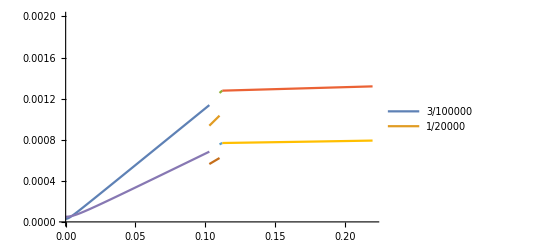

```mathematica
waistfuncs ={};
For[i=1,i<Length[inputWaist]+1,i++,
q0 = -ⅈ π inputWaist[[i]]^2/λ;
AppendTo[waistfuncs,beamPropagate[q0,lenses,λ]](*system input beam*)
]
Plot[Evaluate[waistfuncs],{x,0,d1},PlotRange->{0,0.002},PlotLegends->inputWaist]
```

```mathematica
(waistfuncs[[1,-1]]/.x->d1)
```

0.00131938

```mathematica
(waistfuncs[[2,-1]]/.x->d1)
```

0.000791641